Номер 1
Условие:
Создать таблицу значений функции f(x), разбив отрезок [0; 6] на n равных частей точками x_i (i = OverBar[0,n]). Для полученной таблично заданной в равноотстоящих узлах функции f(x), выполнить следующие действия при n = 6 и n = 10:
а) построить интерполяционный многочлен Лагранжа L_n(x) ,
проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и L_n(x) на одном чертеже);
б) создать таблицу конечных разностей функции f(x) по точкам (x_i, f(x_i)), i = OverBar[0,n];
в) построить второй интерполяционный многочлен Ньютона P_n(x),
проиллюстрировать графически;
г) построить интерполяционный многочлен Ньютона Np_n(x) с помощью функции InterpolatingPolynomial пакета Mathematica,
проиллюстрировать графически;
д) вычислить значения функции f(x) и всех построенных
интерполяционных многочленов L_n(x) , P_n(x) и Np_n(x) в точке
x = 2,4316;
е) построить график погрешности интерполирования многочленом Ньютона R_n(x) = |f(x) - Np_n(x)| на отрезке [0; 6], найти максимум погрешности R_n(x) на отрезке [0, 6] с помощью функции FindMaximum пакета Mathematica;
ж) исследовать зависимость погрешности интерполирования R_n(x) от
числа узлов интерполяции (степени многочлена n).

Функция f(x):

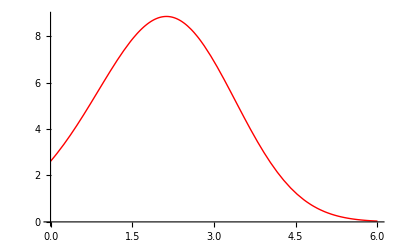

```mathematica
f[x_]= (x + √(π+1))* Exp[-4/39*√(x^5)+5*x/9+1/4];
a=0;b=6;n1=6;n2=10;x0=2.4316;h1=(b-a)/n1;h2=(b-a)/n2;
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

Создадим таблицы значений функции для равноотстоящих узлов на промежутке для n1 и n2:

```mathematica
data1=N[Table[{a+i* h1,f[a+i* h1]},{i,0,n1}]]
```

{{0.,2.61311},{1.,6.13023},{2.,8.81055},{3.,6.91907},{4.,2.68522},{5.,0.470096},{6.,0.0341457}}

```mathematica
data2=N[Table[{a+i *h2,f[a+i *h2]},{i,0,n2}]]
```

{{0.,2.61311},{0.6,4.58895},{1.2,6.88217},{1.8,8.57075},{2.4,8.65092},{3.,6.91907},{3.6,4.29295},{4.2,2.02528},{4.8,0.712835},{5.4,0.183836},{6.,0.0341457}}

```mathematica
{TableForm[data1],TableForm[data2]}
```

{0. | 2.61311
1. | 6.13023
2. | 8.81055
3. | 6.91907
4. | 2.68522
5. | 0.470096
6. | 0.0341457,0. | 2.61311
0.6 | 4.58895
1.2 | 6.88217
1.8 | 8.57075
2.4 | 8.65092
3. | 6.91907
3.6 | 4.29295
4.2 | 2.02528
4.8 | 0.712835
5.4 | 0.183836
6. | 0.0341457}

а) Введём вспомогательные обозначения P1(x) и P2(x):

```mathematica
P1[x_]=∏_(i=0)^n1 (x-data1[[i+1,1]])
P2[x_]=∏_(i=0)^n2 (x-data2[[i+1,1]])
```

(-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x) (0.+x)

(-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)

Используя заданные обозначения, зададим формулы интерполяционного многочлена Лагранжа для n1 и n2:

```mathematica
Ln1[x_]=Sum[data1[[i+1,2]] P1[x]/((x-data1[[i+1,1]]) P1'[data1[[i+1,1]]]),{i,0,n1}]//Simplify
```

2.61311+0.916191 x+4.6762 x^2-2.32529 x^3+0.225577 x^4+0.0284719 x^5-0.00402739 x^6

```mathematica
Ln2[x_]=Sum[data2[[i+1,2]] P2[x]/((x-data2[[i+1,1]]) P2'[data2[[i+1,1]]]),{i,0,n2}]//Simplify
```

2.61311+2.36963 x+2.73186 x^2-3.19862 x^3+2.86476 x^4-1.70431 x^5+0.537607 x^6-0.087452 x^7+0.00647327 x^8-0.0000741012 x^9-0.0000101178 x^10

Изобразим полученные интерполяционные многочлены.
Интерполяционный многочлен Лагранжа для n = 6:

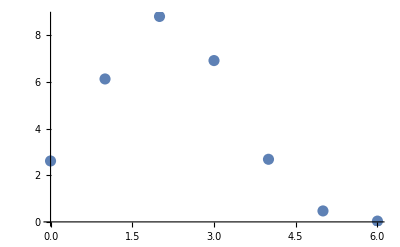

```mathematica
graph1D=ListPlot[data1,PlotStyle->{Darker,PointSize[0.02]}]
```

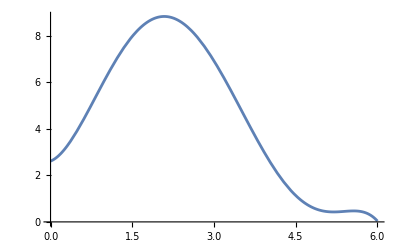

```mathematica
graph1Ln=Plot[Ln1[x],{x,a,b}]
```

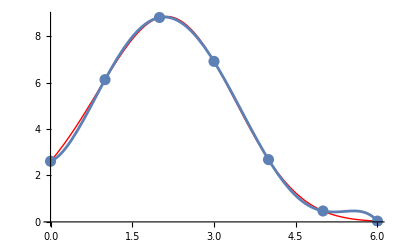

```mathematica
Show[graph,graph1D,graph1Ln]
```

Интерполяционный многочлен Лагранжа для n = 10:

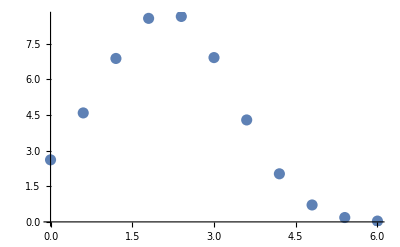

```mathematica
graph2D=ListPlot[data2,PlotStyle->{Darker,PointSize[0.02]}]
```

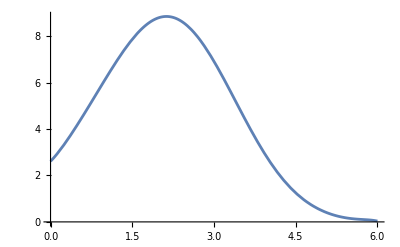

```mathematica
graph2Ln=Plot[Ln2[x],{x,a,b}]
```

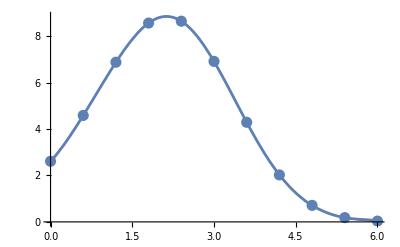

```mathematica
Show[graph,graph2D,graph2Ln]
```

б) Представим таблицу конечных разностей функции f(x) в виде матрицы, каждый столбец которой соответствует конечным разностям соответствующего порядка от 0 до n - 1 (конечные разности 0-го порядка - значения функции в точках  x_i).
Для n = 6:

```mathematica
Array[dif1,{n1+1,n1+1},{0,0}];
```

Поскольку с увеличением порядка конечных разностей их количество уменьшается, заполним пустые клетки таблицы:

```mathematica
For[k=1,k≤n1,k++,
For[i=n1,i≥n1-k,i--,dif1[i,k]=""]];
For[i=0,i≤n1,i++,dif1[i,0]=data1[[i+1,2]]];
For[k=1,k≤n1,k++,
For[i=0,i≤n1-k,i++,
dif1[i,k]=dif1[i+1,k-1]-dif1[i,k-1]]];
diftab1=Array[dif1,{n1+1,n1+1},{0,0}];
PaddedForm[TableForm[diftab1],{n1,n1-1}]
```

2.61311 |  3.51712 | -0.83681 | -3.73498 |  5.96439 | -3.83267 | -2.89972
 6.13023 |  2.68032 | -4.57179 |  2.22941 |  2.13171 | -6.73239 | 
 8.81055 | -1.89147 | -2.34238 |  4.36112 | -4.60068 |  | 
 6.91907 | -4.23386 |  2.01873 | -0.23956 |  |  | 
 2.68522 | -2.21512 |  1.77917 |  |  |  | 
 0.47010 | -0.43595 |  |  |  |  | 
 0.03415 |  |  |  |  |  |

Аналогичным образом заполним таблицу для n = 10:

```mathematica
Array[dif2,{n2+1,n2+1},{0,0}];
For[k=1,k≤n2,k++,
For[i=n2,i≥n2-k,i--,dif2[i,k]=""]];
For[i=0,i≤n2,i++,dif2[i,0]=data2[[i+1,2]]];
For[k=1,k≤n2,k++,
For[i=0,i≤n2-k,i++,
dif2[i,k]=dif2[i+1,k-1]-dif2[i,k-1]]];
diftab2=Array[dif2,{n2+1,n2+1},{0,0}];
PaddedForm[TableForm[diftab2],{n2,n2-1}]
```

2.613107710 |  1.975837993 |  0.317391059 | -0.922043222 | -0.081714132 |  0.881869019 | -0.560685047 | -0.546855160 |  1.449840589 | -1.270011999 | -0.222005389
 4.588945703 |  2.293229052 | -0.604652164 | -1.003757354 |  0.800154887 |  0.321183972 | -1.107540207 |  0.902985429 |  0.179828590 | -1.492017388 | 
 6.882174755 |  1.688576888 | -1.608409518 | -0.203602468 |  1.121338859 | -0.786356235 | -0.204554778 |  1.082814019 | -1.312188798 |  | 
 8.570751644 |  0.080167370 | -1.812011986 |  0.917736391 |  0.334982624 | -0.990911012 |  0.878259242 | -0.229374778 |  |  | 
 8.650919014 | -1.731844616 | -0.894275595 |  1.252719015 | -0.655928388 | -0.112651770 |  0.648884464 |  |  |  | 
 6.919074398 | -2.626120211 |  0.358443420 |  0.596790627 | -0.768580158 |  0.536232693 |  |  |  |  | 
 4.292954187 | -2.267676791 |  0.955234047 | -0.171789531 | -0.232347465 |  |  |  |  |  | 
 2.025277396 | -1.312442744 |  0.783444515 | -0.404136996 |  |  |  |  |  |  | 
 0.712834651 | -0.528998229 |  0.379307519 |  |  |  |  |  |  |  | 
 0.183836423 | -0.149690710 |  |  |  |  |  |  |  |  | 
 0.034145713 |  |  |  |  |  |  |  |  |  |

в) Построим вторые интерполяционные многочлены Ньютона Pn1 (x) и Pn2 (x) для n1 = 6 и n2 = 10 :

```mathematica
q1=(x-b)/h1;Pn1[x_]=dif1[n1,0];P1[q_]=1;
For[k=1,k≤n1,k++,P1[q_]=P1[q1]*(q1+k-1);Pn1[x_]=Pn1[x]+P1[q1]/(k!) dif1[n1-k,k]];
Pn1[x]//Simplify
```

2.61311+0.916191 x+4.6762 x^2-2.32529 x^3+0.225577 x^4+0.0284719 x^5-0.00402739 x^6

```mathematica
q2=(x-b)/h2;Pn2[x_]=dif2[n2,0];P2[q_]=1;
For[k=1,k≤n2,k++,P2[q_]=P2[q2]*(q2+k-1);Pn2[x_]=Pn2[x]+P2[q2]/(k!)dif2[n2-k,k] ];
Pn2[x]//Simplify
```

2.61311+2.36963 x+2.73186 x^2-3.19862 x^3+2.86476 x^4-1.70431 x^5+0.537607 x^6-0.087452 x^7+0.00647327 x^8-0.0000741012 x^9-0.0000101178 x^10

Изобразим полученные интерполяционные многочлены .
Второй интерполяционный многочлен Ньютона для n = 6:

```mathematica
graph1Pn=Plot[Pn1[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graph,graph1D,graph1Pn]
```

-Graphics-

Второй интерполяционный многочлен Ньютона для n = 10 :

```mathematica
graph2Pn=Plot[Pn2[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graph,graph2D,graph2Pn]
```

-Graphics-

г) Интерполяционные многочлены Ньютона функции f(x) для n1 = 6 и n2 = 10, построенные встроенной функцией пакета Mathematica:

```mathematica
Npn1[x_]=InterpolatingPolynomial[data1,x]//Simplify
```

2.61311+0.916191 x+4.6762 x^2-2.32529 x^3+0.225577 x^4+0.0284719 x^5-0.00402739 x^6

```mathematica
Npn2[x_]=InterpolatingPolynomial[data2,x]//Simplify
```

2.61311+2.36963 x+2.73186 x^2-3.19862 x^3+2.86476 x^4-1.70431 x^5+0.537607 x^6-0.087452 x^7+0.00647327 x^8-0.0000741012 x^9-0.0000101178 x^10

Изобразим полученные интерполяционные многочлены .
Интерполяционный многочлен Ньютона для n = 6:

```mathematica
graph1Npn=Plot[Npn1[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graph,graph1D,graph1Npn]
```

-Graphics-

Интерполяционный многочлен Ньютона для n = 10 :

```mathematica
graph2Npn=Plot[Npn2[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graph,graph2D,graph2Npn]
```

-Graphics-

д)

```mathematica
Print["f[x0]=",f[x0]]
```

f[x0]=8.60116

Значения интерполяционных многочленов Лагранжа в точке x0 :

```mathematica
Print["Ln1[x0]=",Ln1[x0],", Ln2[x0]=",Ln2[x0]]
```

Ln1[x0]=8.53244, Ln2[x0]=8.60107

Значения вторых интерполяционных многочленов Ньютона в точке x0:

```mathematica
Print["Pn1[x0]=",Pn1[x0],", Pn2[x0]=",Pn2[x0]]
```

Pn1[x0]=8.53244, Pn2[x0]=8.60107

Значения интерполяционных многочленов Ньютона в точке x0 :

```mathematica
Print["Npn1[x0]=",Npn1[x0],", Npn2[x0]=",Npn2[x0]]
```

Npn1[x0]=8.53244, Npn2[x0]=8.60107

Исходя из полученных графиков и значений в точке x0, отметим, что интерполяционные многочлены, полученные различными способами, либо совпадают полностью, либо имеют незначительные отличия .

e) Исследуем погрешность интерполирования многочленом Ньютона при n = 6.

```mathematica
Rn1[x_]=Abs[f[x]-Npn1[x]];
```

График погрешности Rn1 (x) :

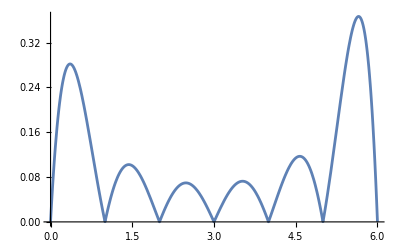

```mathematica
graphErr1=Plot[Rn1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr1=FindMaximum[Rn1[x],{x,a,b}]
```

{0.281977,{x→0.358822}}

Как видно из графика, максимальная погрешность интерполирования многочленом Ньютона при n = 6 находится на отрезке x ϵ [5.4; 6] . В силу погрешности машинного сравнения рациональных чисел функция FindMaximum дала некорректный ответ . Для получения более точного результата сузим промежуток .

```mathematica
maxErr1=FindMaximum[Rn1[x],{x,5.4,b}]
```

{0.366789,{x→5.6539}}

Исследуем погрешность интерполирования многочленом Ньютона при n = 10.

```mathematica
Rn2[x_]=Abs[f[x]-Npn2[x]];
```

График погрешности Rn2 (x) :

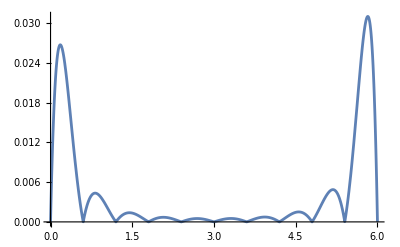

```mathematica
graphErr2=Plot[Rn2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr2=FindMaximum[Rn2[x],{x,a,b}]
```

{0.0267321,{x→0.178828}}

Как видно из графика, максимальная погрешность интерполирования многочленом Ньютона при n = 10 принадлежит отрезку x ϵ [5.4; 6] . В силу погрешности машинного сравнения рациональных чисел функция FindMaximum дала некорректный ответ .
Для получения более точного результата сузим промежуток значений аргумента:

```mathematica
maxErr2=FindMaximum[Rn2[x],{x,5.6,b}]
```

{0.0310142,{x→5.82281}}

ж) Исходя из полученных графиков погрешностей, можно сделать вывод, что с увеличением степени интерполяционного многочлена n погрешность интерполирования уменьшается (значение maxErr1 значительно больше значения maxErr2).